# Lagaris Problem 4: Coupled 1st-Order ODE IVP

Solving the ODE in Mathematica:

```mathematica
de1=ψ1'[x]==Cos[x]+ψ1[x]^2+ψ2[x]-(1+x^2+Sin[x]^2)
```

ψ1'[x]==-1-x^2+Cos[x]-Sin[x]^2+ψ1[x]^2+ψ2[x]

```mathematica
de2=ψ2'[x]==2x-(1+x^2)Sin[x]+ψ1[x] ψ2[x]
```

ψ2'[x]==2 x-(1+x^2) Sin[x]+ψ1[x] ψ2[x]

```mathematica
DSolve[{de1,de2,ψ1[0]==0,ψ2[0]==1},{ψ1[x],ψ2[x]},x]
```

DSolve[{ψ1'[x]==-1-x^2+Cos[x]-Sin[x]^2+ψ1[x]^2+ψ2[x],ψ2'[x]==2 x-(1+x^2) Sin[x]+ψ1[x] ψ2[x],ψ1[0]==0,ψ2[0]==1},{ψ1[x],ψ2[x]},x]

Why is this solution not working?

```mathematica
ψa1[x_]:=Sin[x]
```

```mathematica
ψa2[x_]:=1+x^2
```

```mathematica
FullSimplify[D[ψa1[x],x]]
```

Cos[x]

```mathematica
FullSimplify[D[ψa2[x],x]]
```

2 x

```mathematica
dψa1dx[x_]:=Cos[x]
```

```mathematica
dψa2dx[x_]:=2x
```

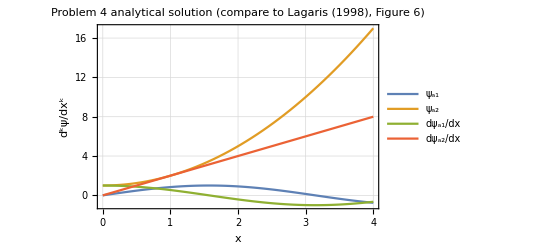

```mathematica
Plot[{ψa1[x],ψa2[x],dψa1dx[x],dψa2dx[x]},{x,0,4},AxesLabel->{"x","d^kψ/dx^k"},PlotLegends->{"ψ_a1","ψ_a2","dψ_a1/dx","dψ_a2/dx"},PlotLabel->"Problem 4 analytical solution (compare to Lagaris (1998), Figure 6)",Frame->True,GridLines->Automatic]
```